```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/johann/Dropbox/projects/approximation

## GSL

If the GNU Scientific Library is compiled, we can call its  function from Mathematica:

```mathematica
gslSin=ForeignFunctionLoad["/usr/local/lib/libgsl","gsl_sf_sin",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

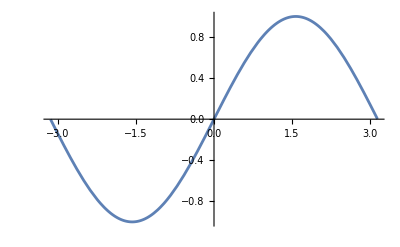

```mathematica
Plot[gslSin[x],{x,-3.14,3.14}]
```

It’s accurate to machine precision, or pretty close.

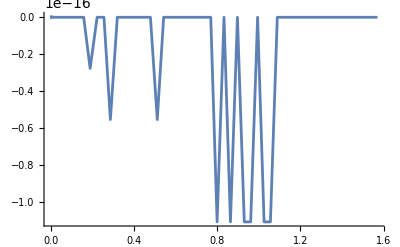

```mathematica
Plot[gslSin[x]-Sin[x],{x,0,Pi/2},WorkingPrecision->24]
```

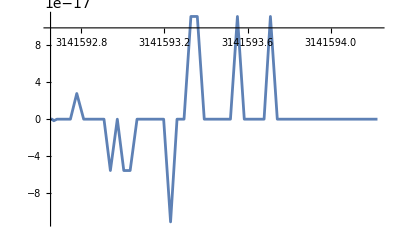

```mathematica
Plot[gslSin[x]-Sin[x],{x,N[π*10^6],N[π*10^6+π/2]},WorkingPrecision->24]
```

```mathematica
RepeatedTiming[gslSin[RandomReal[]],10]
```

{4.58614×10^-6,0.0991604}

## Calling Assembly Language

### sin1.s

This is the most basic approximation, using just the first two terms of the Taylor series, just as a proof that we can write a dynamic library in ARM assembly and call it from C and from Mathematica.

// sin1.s
// Approximate Sin(x) by the Taylor series to degree 3.

.global _sin_1
.p2align 2			// Make sure everything is aligned properly

.text

_sin_1:
        fmul    d1, d0, d0              // d1 = d0^2
        fmul    d1, d1, d0              // d1 = d0^3
        fmov    d2, #6
        fdiv    d1, d1, d2              // d1 = d0^3/6
        fsub    d0, d0, d1              // d0 = d0 - d0^3/6
        ret

```mathematica
sin1=ForeignFunctionLoad["./sin/libsin1","sin_1",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin1[0]
```

0.

```mathematica
sin1[N[Pi/2]]
```

0.924832

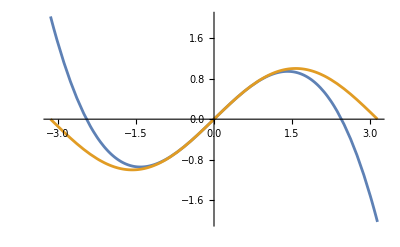

```mathematica
Plot[{sin1[x],Sin[x]},{x,-Pi,Pi}]
```

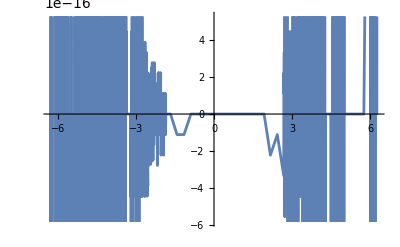

```mathematica
Plot[sin1[x]-(x-x^3/6),{x,-2π,2π},WorkingPrecision->24]
```

```mathematica
Clear[sin2]
sin2=ForeignFunctionLoad["./sin/libsin2","sin_2",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin2[0.0]
```

3.1516×10^-17

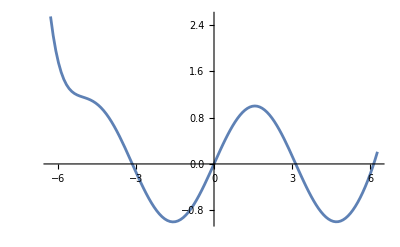

```mathematica
Plot[sin2[x],{x,-2Pi,2Pi}]
```

```mathematica
sin3=ForeignFunctionLoad["./sin/libsin3","sin_3",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

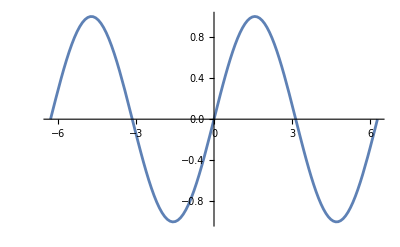

```mathematica
Plot[sin3[x],{x,-2Pi,2Pi}]
```

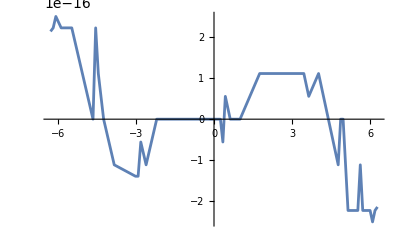

```mathematica
Plot[Sin[x]-sin3[x],{x,-2Pi,2Pi}]
```

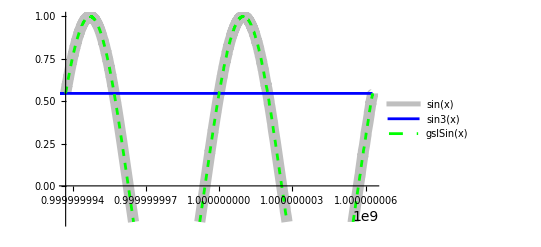

```mathematica
Plot[{Sin[x],sin3[x],gslSin[x]},{x,10^9-2Pi,10^9+2Pi},
PlotLegends->"Expressions",
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}},
PlotStyle->{{Thickness[0.02],Opacity[0.5],Gray},{Blue},{Dashed,Green}}]
```

```mathematica
|
```

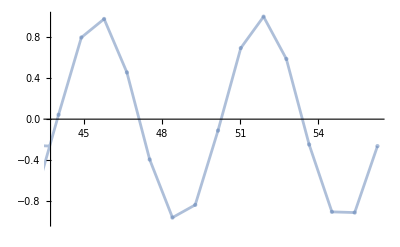

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

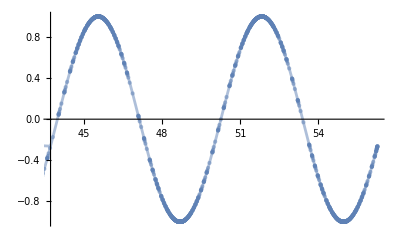

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]},MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

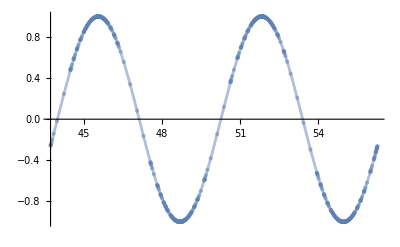

```mathematica
Plot[gslSin[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

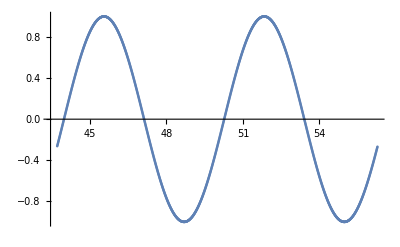

```mathematica
ListPlot[Table[{x,sin3[x]},{x,50-2Pi,50+2Pi,0.01}]]
```

```mathematica
reduce=ForeignFunctionLoad["./sin/libreduce","reduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

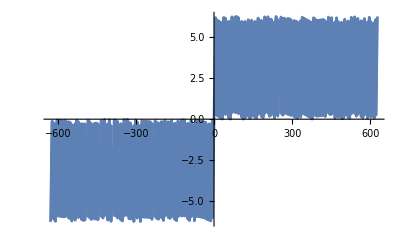

```mathematica
Plot[reduce[x],{x,-200Pi,200Pi}]
```

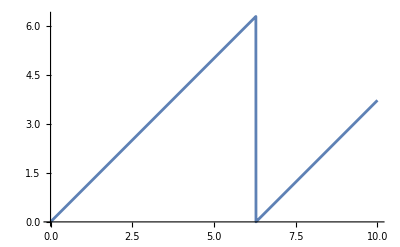

```mathematica
Plot[reduce[x],{x,0,10}]
```

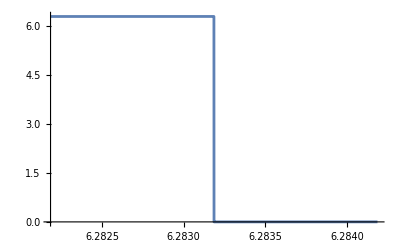

```mathematica
Plot[reduce[x],{x,2Pi-0.001,2Pi+0.001}]
```

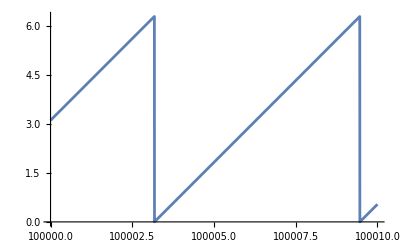

```mathematica
Plot[reduce[x],{x,100000,100010}]
```